```mathematica
filename="D:\\Document\\Seafile\\Experiment\\Artiq\\Sequence\\data\\Rabi_AOM_fre_Scan238.0-242.0.csv";
data=Import[filename];
Dimensions[data]
```

{16000,4}

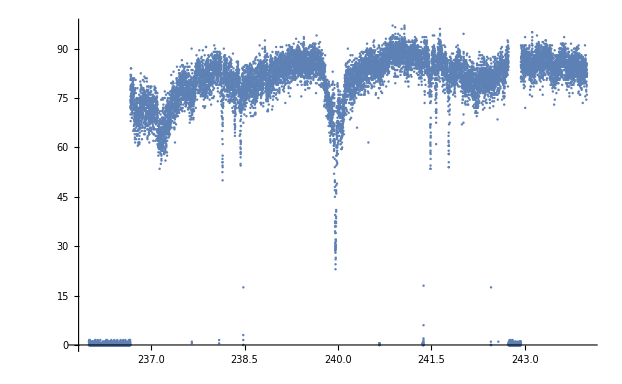

```mathematica
ListPlot[data[[;;,1;;2]]]
```

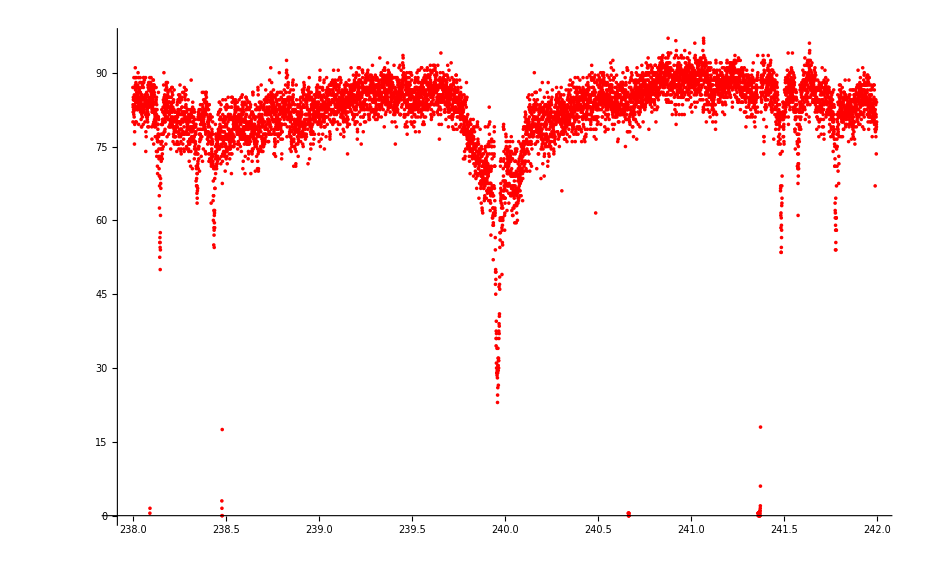

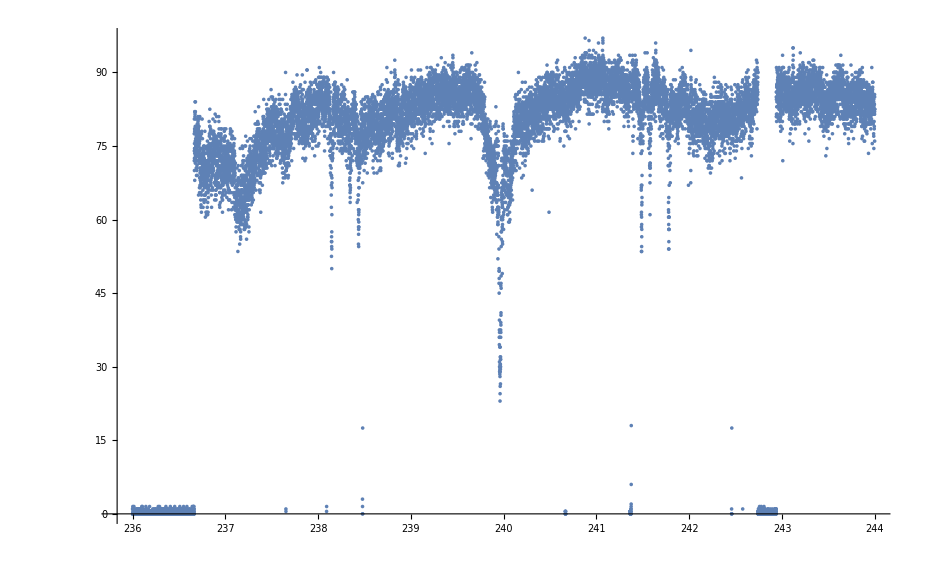

```mathematica
start = 4000;
end = 12000;
Clear[data1];
data1 = data[[start;;end,1;;2]];
ListPlot[data1,PlotStyle->Red]
ListPlot[data[[;;,1;;2]]]
```

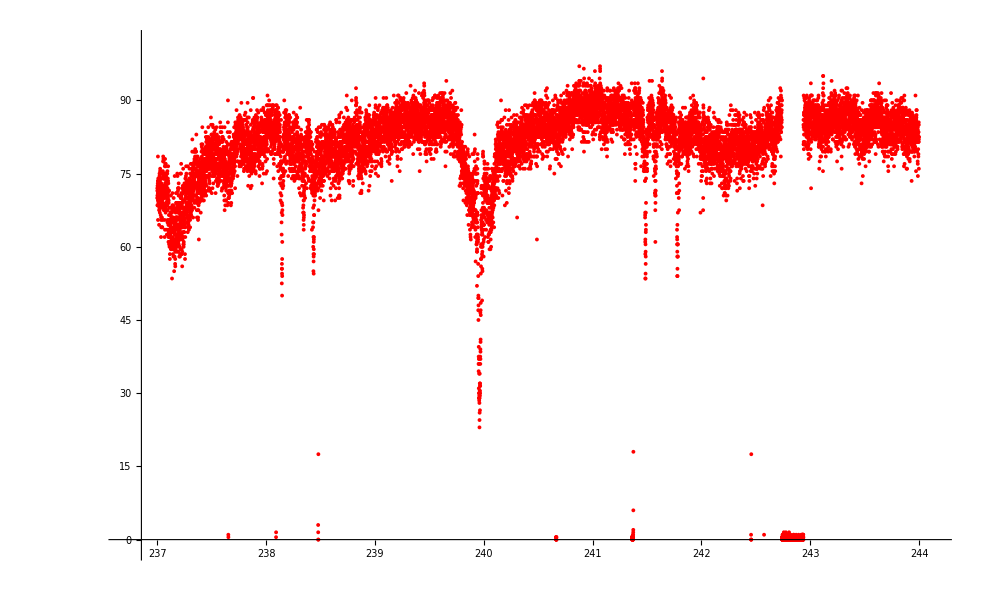

```mathematica
carrier = 239.96;
redx = 238.431;
red
```